#### Preamble

```mathematica
saveTask=CreateScheduledTask[FrontEndExecute[FrontEndToken["Save"]],15*60]; (*Saves nb each 15 minutes*)
StartScheduledTask[saveTask]
```

ScheduledTaskObject[…]

```mathematica
SetDirectory[NotebookDirectory[]]
<<"MaTeX`"
<<"~/Documents/Wolfram/Wolfram_scripts/Optics_Mie.wls"
<<"~/Documents/Wolfram/Wolfram_scripts/Nano_CSM_SDistAll.wls"
<<"~/Documents/Wolfram/Wolfram_scripts/Nano_CSM_Biosensor.wls"
<<"~/Documents/Wolfram/Wolfram_scripts/Optical_functions/Au_JohnsnChristy.wls"
```

/home/juanathan/Documents/Collaborations/En progreso/2022-06-INAOE-CSM/5-SustratoEmbedding-Fit

```mathematica
fs = 10;
texStyle={FontFamily->"Latin Modern Math",FontSize->fs,Black};
colors=(("DefaultPlotStyle"/.(Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);
colors = Flatten@Prepend[colors,{Red,Darker[Green]}]
```

{RGBColor[1, 0, 0],RGBColor[0, Rational[2, 3], 0],RGBColor[0.9, 0.36, 0.054],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8],RGBColor[0.71788, 0.568653, 0.],RGBColor[0.70743, 0.224, 0.542415],RGBColor[0.287228, 0.490217, 0.664674],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]}

```mathematica
em[name_String, size_ : 7] := 
  ResourceFunction["PolygonMarker"][name, 
   Offset[size], {Dynamic@
     EdgeForm[{CurrentValue["Color"], JoinForm["Round"], 
       AbsoluteThickness[1], Opacity[1]}], FaceForm[White]}, 
   ImagePadding -> 6];
```

### Incrustamiento

```mathematica
graphsOpts
```

graphsOpts

```mathematica
scaleFactor[h_]:=0.5 - 0.75*h + 0.25*h*h*h ; (*h -> Incrustation factor: h/a. h Distance between center and interface, a AuNP radius*)
radiusM = {5.78, 7.30};
radiusF = {3.3, 4.5};

graphsOpts = {Mesh-> None,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 685*2/5};
graphsH = MapIndexed[ Plot[scaleFactor[h]-#1 ,{h,-1,1},Evaluate[graphsOpts],PlotStyle->First[#2]]& ,((radiusF/radiusM)^3)];
roots = FindRoot[scaleFactor[h]-#^3 == 0, {h,.1} ] & /@ (radiusF/radiusM)

fplot = Show[graphsH, ListPlot[(Callout[{h,0},h] /. roots),PlotStyle->PointSize[.025]],
            FrameLabel->{MaTeX["h/a",FontSize->fs],MaTeX["f(h/a)",FontSize->fs]}]
            
(h /. roots)*radiusM
Export["S1-Embedding.svg",fplot]
Export["S1-Embedding-Labels.svg", SwatchLegend[{Blue,Red},{Style["3.3 nm/ 5.78 nm",texStyle],Style["4.5 nm/7.30 nm",texStyle]}]]
```

{{h→0.448624},{h→0.371421}}

-Graphics-

{2.59304,2.71137}

S1-Embedding.svg

S1-Embedding-Labels.svg

### Mie vs Embedding

```mathematica
radius = {5.78, 7.3};
nNP = JohnsonChristyAuRefSize[#1, #2] &;

scaQ[lda_,radius_]:= Map[MieScatteringQ[{1., nNP[#, radius]}, #, radius]&, lda]
extQ[lda_,radius_]:= Map[MieExtinctionQ[{1., nNP[#, radius]}, #, radius]&, lda]
```

```mathematica
Partition[#,3] &@ FileNames["*CabsCsca.csv",{"5-78nm","7-30nm"}]
data = Import[#,"Data"] & /@ FileNames["*CabsCsca.csv",{"5-78nm","7-30nm"}]; (*Import both files*)
data = Transpose[Drop[#,5,{1}]] & /@ data; (*[[radius, lda, abs, sca]]*)
 
wlen = data[[1,1,;;-11]] (*create lda*);
wlenMie = Range[#1,#2,.25]&@@wlen[[{1,-1}]];

data = data[[;;,{2,3},;;-11]]; (* [[radius, abs, sca]]*)
data = Apply[Plus,data,{1}] (*[[radius, abs + sca = ext]]*);
dataMie = extQ[wlenMie,#] & /@ radius;
```

{{5-78nm/MasAir-CabsCsca.csv,5-78nm/MasBK7-CabsCsca.csv,5-78nm/Mitad-CabsCsca.csv},{7-30nm/MasAir-CabsCsca.csv,7-30nm/MasBK7-CabsCsca.csv,7-30nm/Mitad-CabsCsca.csv}}

#### abs(h/a)<= 0.44 All

```mathematica
plots = ConstantArray[0,4];

graphsOptsMie = {Mesh-> None,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 685*2/5, PlotStyle-> (Directive[#]&/@colors)};
graphsOptsFEM = {Mesh-> All,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 685*2/5, PlotStyle-> (Directive[#,Thin]&/@colors),
                PlotMarkers-> em[#,2.5]&/@{"Disk"}};
                
extMie = Transpose[{wlenMie,#}] & /@ dataMie;
maxMie = MaximalBy[#,Last] & /@ extMie
extFEM = Transpose[{wlen,#}] & /@ data;
maxFEM = MaximalBy[#,Last] & /@ extFEM

plots[[1]] = ListLinePlot[#,Evaluate[graphsOptsMie]]& @ extMie;
plots[[2]] = ListLinePlot[#,Evaluate[graphsOptsFEM]]& @ extFEM;
plots[[3]] = ListPlot[Callout[#,NumberForm[First[#],{4,1}],Right,LabelStyle->texStyle]& /@ Flatten[maxMie,1], PlotStyle-> Directive[Magenta,PointSize[.025]] ];
plots[[4]] = ListPlot[Callout[#,NumberForm[First[#],{4,1}],Right,LabelStyle->texStyle]& /@ Flatten[maxFEM,1],PlotStyle-> Directive[Magenta,PointSize[.025]]  ];
```

{{{509.75,0.20717}},{{509.5,0.272552}}}

{{{520.,0.270178}},{{528,0.600891}},{{523.5,0.431966}},{{521,0.393963}},{{528,0.770686}},{{523.75,0.578933}}}

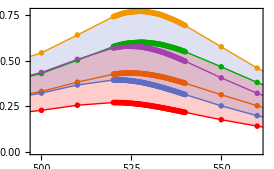

```mathematica
plots[[2]] = ListLinePlot[#,Evaluate[graphsOptsFEM],Filling->{1->{2},4->{5}}]& @ extFEM
```

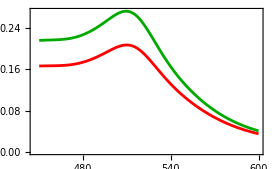
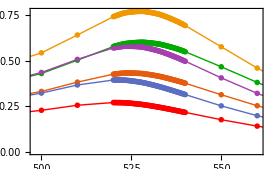
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
plots
```

```mathematica
fplot = Show[plots[[;;]],AspectRatio->1/GoldenRatio,ImageSize-> 250*1.05, PlotRange->All, FrameLabel -> (Style[#,texStyle]&/@{"Wavelength [nm]","Extinction Efficiencies"}) ]
(*Export["Mie-vs-Comsol-Embedded.svg",fplot]*)
```

-Graphics-

#### abs(h/a)<= 0.44 First monolayer

```mathematica
ResourceFunction["PolygonMarker"]
allShapes = ResourceFunction["PolygonMarker"][All]
```

{TripleCross,Y,UpTriangle,UpTriangleTruncated,DownTriangle,DownTriangleTruncated,LeftTriangle,LeftTriangleTruncated,RightTriangle,RightTriangleTruncated,ThreePointedStar,Cross,DiagonalCross,Diamond,Square,FourPointedStar,DiagonalFourPointedStar,FivefoldCross,Pentagon,FivePointedStar,FivePointedStarSlim,FivePointedStarThick,DancingStar,DancingStarRight,DancingStarThick,DancingStarThickRight,SixfoldCross,Hexagon,SixPointedStar,SixPointedStarSlim,SixfoldPinwheel,SixfoldPinwheelRight,SevenfoldCross,SevenPointedStar,SevenPointedStarNeat,SevenPointedStarSlim,SevenfoldPinwheel,SevenfoldPinwheelRight,EightfoldCross,Disk,H,I,N,Z,S,Sw,Sl}

```mathematica
plots = ConstantArray[0,4];

graphsOptsMie = {Mesh-> None,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 685*2/5, PlotStyle-> (Directive[#]&/@colors)};
graphsOptsFEM = {Mesh-> All,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 685*2/5, PlotStyle-> (Directive[#,Thin]&/@colors[[{1,1,1}]]),
                PlotMarkers-> (em[#,2.5]&/@{"Disk","Diamond","Square"})};
                
extMie = Transpose[{wlenMie,#}] & /@ dataMie;
maxMie = MaximalBy[#,Last] & /@ extMie
extFEM = Transpose[{wlen,#}] & /@ data;
maxFEM = MaximalBy[#,Last] & /@ extFEM

plots[[1]] = ListLinePlot[#,Evaluate[graphsOptsMie]]& @ extMie[[1]];
plots[[2]] = ListLinePlot[#,Evaluate[graphsOptsFEM],Filling->{1->{2}}]& @ extFEM[[;;3]];
plots[[3]] = ListPlot[Callout[#,ToString@NumberForm[First[#],{4,1}]<>" nm",Right,LabelStyle->texStyle]& /@ Flatten[maxMie,1], PlotStyle-> Directive[Magenta,PointSize[.025]] ];
plots[[4]] = ListPlot[Callout[#,ToString@NumberForm[First[#],{4,1}]<>" nm",Right,LabelStyle->texStyle]& /@ Flatten[maxFEM,1][[;;3]],PlotStyle-> Directive[Magenta,PointSize[.025]]  ];
```

{{{509.75,0.20717}},{{509.5,0.272552}}}

{{{520.,0.270178}},{{528,0.600891}},{{523.5,0.431966}},{{521,0.393963}},{{528,0.770686}},{{523.75,0.578933}}}

```mathematica
fplot = Show[plots[[;;]],AspectRatio->1,ImageSize-> 200, PlotRange->All, FrameLabel -> (Style[#,texStyle]&/@{"Wavelength [nm]","Extinction Efficiencies"}) ]
Export["Mie-vs-Comsol-Embedded-5-78.svg",fplot]
```

-Graphics-

Mie-vs-Comsol-Embedded-5-78.svg

#### abs(h/a)<= 0.44 Second monolayer

```mathematica
plots = ConstantArray[0,4];

graphsOptsMie = {Mesh-> None,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 685*2/5, PlotStyle-> (Directive[#]&/@colors[[{2}]])};
graphsOptsFEM = {Mesh-> All,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 685*2/5, PlotStyle-> (Directive[#,Thin]&/@colors[[{2,2,2}]]),
                PlotMarkers-> (em[#,2.5]&/@{"Disk","Diamond","Square"})};
                
extMie = Transpose[{wlenMie,#}] & /@ dataMie;
maxMie = MaximalBy[#,Last] & /@ extMie
extFEM = Transpose[{wlen,#}] & /@ data;
maxFEM = MaximalBy[#,Last] & /@ extFEM

plots[[1]] = ListLinePlot[#,Evaluate[graphsOptsMie]]& @ extMie[[2]];
plots[[2]] = ListLinePlot[#,Evaluate[graphsOptsFEM],Filling->{1->{2}}]& @ extFEM[[4;;]];
plots[[3]] = ListPlot[Callout[#,ToString@NumberForm[First[#],{4,1}]<>" nm",Right,LabelStyle->texStyle]& /@ Flatten[maxMie,1], PlotStyle-> Directive[Magenta,PointSize[.025]] ];
plots[[4]] = ListPlot[Callout[#,ToString@NumberForm[First[#],{4,1}]<>" nm",Right,LabelStyle->texStyle]& /@ Flatten[maxFEM,1][[4;;]],PlotStyle-> Directive[Magenta,PointSize[.025]]  ];
```

{{{509.75,0.20717}},{{509.5,0.272552}}}

{{{520.,0.270178}},{{528,0.600891}},{{523.5,0.431966}},{{521,0.393963}},{{528,0.770686}},{{523.75,0.578933}}}

```mathematica
fplot = Show[plots[[;;]],AspectRatio->1,ImageSize-> 200, PlotRange->All, FrameLabel -> (Style[#,texStyle]&/@{"Wavelength [nm]","Extinction Efficiencies"}) ]
Export["Mie-vs-Comsol-Embedded-7-30.svg",fplot]
```

-Graphics-

Mie-vs-Comsol-Embedded-7-30.svg

#### abs(h/a) == 0

```mathematica
plots = ConstantArray[0,4];

graphsOptsMie = {Mesh-> None,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 685*2/5, PlotStyle-> (Directive[#]&/@colors)};
graphsOptsFEM = {Mesh-> All,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 685*2/5, PlotStyle-> (Directive[#,Thin]&/@colors),
                PlotMarkers-> em[#,2.5]&/@{"Disk"}};
                
extMie = Transpose[{wlenMie,#}] & /@ dataMie;
maxMie = MaximalBy[#,Last] & /@ extMie
extFEM = Transpose[{wlen,#}] & /@ data[[{2,5}]];
maxFEM = MaximalBy[#,Last] & /@ extFEM

plots[[1]] = ListLinePlot[#,Evaluate[graphsOptsMie]]& @ extMie;
plots[[2]] = ListLinePlot[#,Evaluate[graphsOptsFEM]]& @ extFEM;
plots[[3]] = ListPlot[Callout[#,NumberForm[First[#],{5,2}],Right,LabelStyle->texStyle]& /@ Flatten[maxMie,1], PlotStyle-> Directive[Magenta,PointSize[.025]] ];
plots[[4]] = ListPlot[Callout[#,NumberForm[First[#],{5,2}],Right,LabelStyle->texStyle]& /@ Flatten[maxFEM,1],PlotStyle-> Directive[Magenta,PointSize[.025]]  ];
```

{{{509.75,0.20717}},{{509.5,0.272552}}}

{{{528,0.600891}},{{528,0.770686}}}

```mathematica
fplot = Show[plots[[;;]],AspectRatio->1/GoldenRatio,ImageSize-> 250*1.05, PlotRange->All, FrameLabel -> (Style[#,texStyle]&/@{"Wavelength [nm]","Extinction Efficiencies"}) ]
Export["Mie-vs-Comsol-Embedded.svg",fplot]
```

-Graphics-

Mie-vs-Comsol-Embedded.svg

### Mie vs Embedded Dimmer

```mathematica
radius = {5.78, 7.3};
nNP = JohnsonChristyAuRefSize[#1, #2] &;

scaQ[lda_,radius_]:= Map[MieScatteringQ[{1., nNP[#, radius]}, #, radius]&, lda]
extQ[lda_,radius_]:= Map[MieExtinctionQ[{1., nNP[#, radius]}, #, radius]&, lda]
```

```mathematica
FileNames["*nm.csv","7-30nm-Dimmer"]
data = Import[#,"Data"] & /@ FileNames["*nm.csv","7-30nm-Dimmer"]; (*Import both files*)
data = Transpose[Drop[#,5,{1}]] & /@ data; (*[[radius, lda, abs, sca]]*)
 
wlen = data[[1,1,;;-11]] (*create lda*);
wlenMie = Range[#1,#2,.25]&@@wlen[[{1,-1}]];

data = data[[;;,{2,3},;;-11]]; (* [[radius, abs, sca]]*)
data = Apply[Plus,data,{1}] (*[[radius, abs + sca = ext]]*);
dataMie = extQ[wlenMie,#]*Pi*#*# & /@ radius[[{2}]];
```

{7-30nm-Dimmer/Mitad-Dimmer-7-30nm-04nm.csv,7-30nm-Dimmer/Mitad-Dimmer-7-30nm-06nm.csv,7-30nm-Dimmer/Mitad-Dimmer-7-30nm-08nm.csv,7-30nm-Dimmer/Mitad-Dimmer-7-30nm-10nm.csv,7-30nm-Dimmer/Mitad-Dimmer-7-30nm-12nm.csv,7-30nm-Dimmer/Mitad-Dimmer-7-30nm-14nm.csv}

#### Figure

```mathematica
plots = ConstantArray[0,4];

graphsOptsMie = {Mesh-> None,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 685*2/5, PlotStyle-> (Directive[#]&/@colors)};
graphsOptsFEM = {Mesh-> All,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 685*2/5, PlotStyle-> (Directive[#,Thin]&/@colors),
                PlotMarkers-> em[#,2.5]&/@{"Disk"}};
                
extMie = Transpose[{wlenMie,#}] & /@ dataMie;
maxMie = MaximalBy[#,Last] & /@ extMie
extFEM = Transpose[{wlen,#}] & /@ data;
maxFEM = MaximalBy[#,Last] & /@ extFEM

plots[[1]] = ListLinePlot[#,Evaluate[graphsOptsMie]]& @ extMie;
plots[[2]] = ListLinePlot[#,Evaluate[graphsOptsFEM]]& @ extFEM;
plots[[3]] = ListPlot[Callout[#,NumberForm[First[#],{5,2}],Right,LabelStyle->texStyle]& /@ Flatten[maxMie,1], PlotStyle-> Directive[Magenta,PointSize[.025]] ];
plots[[4]] = ListPlot[Callout[#,NumberForm[First[#],{5,2}],Right,LabelStyle->texStyle]& /@ Flatten[maxFEM,1],PlotStyle-> Directive[Magenta,PointSize[.025]]  ];
```

{{{509.5,45.6295}}}

{{{533,269.779}},{{530.25,245.852}},{{528,232.006}},{{528,222.834}},{{528,216.372}},{{527.,211.753}}}

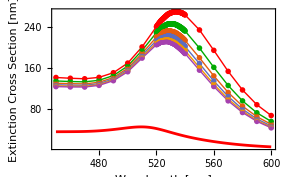

Mie-vs-Comsol-EmbeddedDimmer.svg

```mathematica
fplot = Show[plots[[{1,2}]] ,AspectRatio->1/GoldenRatio,ImageSize-> 250*1.15, PlotRange->All, FrameLabel -> (Style[#,texStyle]&/@{"Wavelength [nm]","Extinction Cross Section [nm]"}) ]
Export["Mie-vs-Comsol-EmbeddedDimmer.svg",fplot]
```

```mathematica
leg = SwatchLegend[colors,(Style[#,texStyle]&/@ Range[4,14,2]),LegendLayout->{"Row",2},LegendLabel->Style["Gap [nm]",texStyle]]
Export["Mie-vs-Comsol-EmbeddedDimmer-label.svg",leg]
```

Mie-vs-Comsol-EmbeddedDimmer-label.svg